```mathematica
C1quWH3=List[-1,-0.8,-0.6,-0.4,-0.5,-0.2,0,0.2,0.4,0.5,0.6,0.8,1]
```

{-1,-0.8,-0.6,-0.4,-0.5,-0.2,0,0.2,0.4,0.5,0.6,0.8,1}

```mathematica
DecayWidth0=2.223847589352296*^-34 (5.401042036315467*^33+1.1125539313316179*^31 (0.+C1quWH3)+5.880534716675024*^16 (0.+1.281593085401099*^12 C1quWH3)+3.5650468051664695*^15 (0.+1.8846957138251458*^12 C1quWH3^2)-1.0386047760439678*^14 (-2.537469185057358*^18+1.0140194455965502*^10 (340000.+60624.53462024999 C1quWH3))-4.037192428791325*^12 (0.+59859.576 (2.230152*^14+1.2511109339285323*^7 (340000.+60624.53462024999 C1quWH3)))) ;
```

```mathematica
DecayWidth0
```

{1.24499,1.24548,1.24596,1.24645,1.24621,1.24694,1.24742,1.24791,1.2484,1.24864,1.24889,1.24937,1.24986}

```mathematica
AAA=Transpose[{C1quWH3,DecayWidth0}]
```

{{-1,1.24499},{-0.8,1.24548},{-0.6,1.24596},{-0.4,1.24645},{-0.5,1.24621},{-0.2,1.24694},{0,1.24742},{0.2,1.24791},{0.4,1.2484},{0.5,1.24864},{0.6,1.24889},{0.8,1.24937},{1,1.24986}}

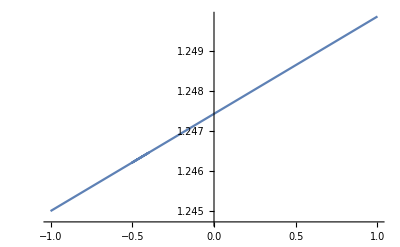

```mathematica
ListLinePlot[AAA,PlotRange->All]
```

```mathematica
DecayWidthtotal=6.352303516574528*^-44  (7.199700306846803*^15 (0.-7.120799999999999*^8 (2.15748818212032*^9 (60624.53462024999 C1quWH3+340000.)+6.5883646444213016*^16))-8.119831137266688*^13 (-8.877502173874452*^14 (60624.53462024999 C1quWH3+340000.)^2-2.3736719132375587*^22 (60624.53462024999 C1quWH3+340000.)-2.4161764036888796*^29)-5.180590245435038*^17 (1.2353902766180376*^10 (60624.53462024999 C1quWH3+340000.)^2-(6.724686239999999*^24+0. ⅈ))-1.4133614093050071*^22 (179578.728 (50812.62258538719 (1.4927003226465262*^7 C1quWH3+8.371497*^7)+2.230152*^14)-2.197344983052719*^20)+4.6254883003821047*^42) ;
```

```mathematica
DecayWidthtotal
```

{1.93502+0. ⅈ,1.9365+0. ⅈ,1.93798+0. ⅈ,1.93946+0. ⅈ,1.93872+0. ⅈ,1.94095+0. ⅈ,1.94243+0. ⅈ,1.94392+0. ⅈ,1.94541+0. ⅈ,1.94615+0. ⅈ,1.9469+0. ⅈ,1.94839+0. ⅈ,1.94988+0. ⅈ}

```mathematica
Transpose[{C1quWH3,DecayWidthtotal}]
```

{{-1,1.93502+0. ⅈ},{-0.8,1.9365+0. ⅈ},{-0.6,1.93798+0. ⅈ},{-0.4,1.93946+0. ⅈ},{-0.5,1.93872+0. ⅈ},{-0.2,1.94095+0. ⅈ},{0,1.94243+0. ⅈ},{0.2,1.94392+0. ⅈ},{0.4,1.94541+0. ⅈ},{0.5,1.94615+0. ⅈ},{0.6,1.9469+0. ⅈ},{0.8,1.94839+0. ⅈ},{1,1.94988+0. ⅈ}}

```mathematica
F0=DecayWidth0/DecayWidthtotal
```

{0.643399+0. ⅈ,0.643159+0. ⅈ,0.642918+0. ⅈ,0.642677+0. ⅈ,0.642798+0. ⅈ,0.642437+0. ⅈ,0.642197+0. ⅈ,0.641956+0. ⅈ,0.641716+0. ⅈ,0.641595+0. ⅈ,0.641475+0. ⅈ,0.641235+0. ⅈ,0.640995+0. ⅈ}

```mathematica
F00=Transpose[{C1quWH3,F0}]
```

{{-1,0.643399+0. ⅈ},{-0.8,0.643159+0. ⅈ},{-0.6,0.642918+0. ⅈ},{-0.4,0.642677+0. ⅈ},{-0.5,0.642798+0. ⅈ},{-0.2,0.642437+0. ⅈ},{0,0.642197+0. ⅈ},{0.2,0.641956+0. ⅈ},{0.4,0.641716+0. ⅈ},{0.5,0.641595+0. ⅈ},{0.6,0.641475+0. ⅈ},{0.8,0.641235+0. ⅈ},{1,0.640995+0. ⅈ}}

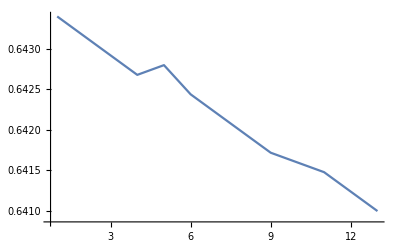

```mathematica
ListLinePlot[F0,PlotRange->All]
```

```mathematica
Table[DecayWidthtotal,{C1quWH3,-1,1}]
```

{{1.93502+0. ⅈ,1.9365+0. ⅈ,1.93798+0. ⅈ,1.93946+0. ⅈ,1.93872+0. ⅈ,1.94095+0. ⅈ,1.94243+0. ⅈ,1.94392+0. ⅈ,1.94541+0. ⅈ,1.94615+0. ⅈ,1.9469+0. ⅈ,1.94839+0. ⅈ,1.94988+0. ⅈ},{1.93502+0. ⅈ,1.9365+0. ⅈ,1.93798+0. ⅈ,1.93946+0. ⅈ,1.93872+0. ⅈ,1.94095+0. ⅈ,1.94243+0. ⅈ,1.94392+0. ⅈ,1.94541+0. ⅈ,1.94615+0. ⅈ,1.9469+0. ⅈ,1.94839+0. ⅈ,1.94988+0. ⅈ},{1.93502+0. ⅈ,1.9365+0. ⅈ,1.93798+0. ⅈ,1.93946+0. ⅈ,1.93872+0. ⅈ,1.94095+0. ⅈ,1.94243+0. ⅈ,1.94392+0. ⅈ,1.94541+0. ⅈ,1.94615+0. ⅈ,1.9469+0. ⅈ,1.94839+0. ⅈ,1.94988+0. ⅈ}}